```mathematica
K=6;
L=6;
M=6;
KLM=Max[K,L,M];
Array[h,K+1,0];
Array[b,L+1,0];
Array[g,M+1,0];
H1=Sum[h[Abs[i]]*x^(i+KLM),{i,0,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-3,-K,-3}];
H2=Sum[h[Abs[i]]*x^(i+KLM),{i,2,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-1,-K,-3}];
H3=Sum[h[Abs[i]]*x^(i+KLM),{i,1,K,3}]+Sum[h[Abs[i]]*x^(i+KLM),{i,-2,-K,-3}];
B1=-Sum[b[Abs[i]]*x^(i+KLM),{i,0,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-3,-L,-3}];
B2=-Sum[b[Abs[i]]*x^(i+KLM),{i,2,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-1,-L,-3}];
B3=-Sum[b[Abs[i]]*x^(i+KLM),{i,1,L,3}]+Sum[b[Abs[i]]*x^(i+KLM),{i,-2,-L,-3}];
G1=Sum[g[Abs[i]]*x^(i+KLM),{i,0,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-3,-M,-3}];
G2=Sum[g[Abs[i]]*x^(i+KLM),{i,2,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-1,-M,-3}];
G3=Sum[g[Abs[i]]*x^(i+KLM),{i,1,M,3}]+Sum[g[Abs[i]]*x^(i+KLM),{i,-2,-M,-3}];
HGDet={{H1,B1,G1},{H2,B2,G2},{H3,B3,G3}};
f=Det[HGDet];
ff=CoefficientList[f,x];
HGDetH={{1,B1,G1},{1,B2,G2},{1,B3,G3}};
fh=Det[HGDetH];
ffh=CoefficientList[fh,x];
Length[ffh];
HGDetB={{H1,1,G1},{H2,1,G2},{H3,1,G3}};
fb=Det[HGDetB];
ffb=CoefficientList[fb,x];
HGDetG={{H1,B1,1},{H2,B2,1},{H3,B3,1}};
fg=Det[HGDetG];
ffg=CoefficientList[fg,x];
K1=Length[ffh]/2-1;
Array[kh,K1+1,0];
For[i=K1+1;j=Length[ffh],i>0,i--;j--,kh[i-1]=-ffh[[j]]];
M1=Length[ffg]/2-1;
Array[kg,M1+1,0];
For[i=M1+1;j=Length[ffg],i>0,i--;j--,kg[i-1]=-ffg[[j]]];
L1=Length[ffb]/2-1;
Array[kb,L1+1,0];
For[i=L1+1;j=Length[ffb],i>0,i--;j--,kb[i-1]=-ffb[[j]]];
Print["(K, L, M)    = (",K,", ", L,", ",M, ")  (",2*K+1,", ", 2*L+1,", ",2*M+1, ")"]
Print["(K1, L1, M1) = (",K1,", ", L1,", ",M1, ")  (",2*K1+1,", ", 2*L1+1,", ",2*M1+1, ")"]
Print["Длина детерминанта - ",Length[ff]]
Print["Середина детерминанта, равная 1, - ",Length[ff]/2-2]
Print["Количество уравнений - ",K+L+M+3]
```

(K, L, M)    = (6, 6, 6)  (13, 13, 13)

(K1, L1, M1) = (11, 11, 11)  (23, 23, 23)

Длина детерминанта - 34

Середина детерминанта, равная 1, - 15

Количество уравнений - 21

```mathematica
s=2^(2/3);
aa=0.07;
NSLv=NSolve[{
b[0]==0,
ff[[Length[ff]]]==0,
ff[[Length[ff]-3]]==0,
ff[[Length[ff]-6]]==0,
ff[[Length[ff]-9]]==0,
ff[[Length[ff]-12]]==0,
ff[[Length[ff]-15]]==-1,

Sum[h[Abs[i]]*(-1)^i,{i,-K,K}]==0,
(*Sum[g[Abs[i]],{i,-M,M}]==0,*)
Sum[kh[Abs[i]],{i,-K1,K1}]==s,
Sum[kh[Abs[i]]*(-1)^i,{i,-K1,K1}]==0,
Sum[kg[Abs[i]],{i,-M1,M1}]==0,
Sum[kg[Abs[i]]*(-1)^i,{i,-M1,M1}]==s,

Sum[i^2*kh[i],{i,1,K1}]==0,
Sum[i^4*kh[i],{i,1,K1}]==0,
Sum[i^2*kh[i]*(-1)^(i-1),{i,1,K1}]==0,
Sum[i^4*kh[i]*(-1)^(i-1),{i,1,K1}]==0,

Sum[i^2*kg[i],{i,1,M1}]==0,
Sum[i^2*kg[i]*(-1)^(i-1),{i,1,M1}]==0,

Sum[i*kb[i],{i,1,L1}]==0,
(*Sum[i^3*kb[i],{i,1,L1}]==0,*)
Sum[i*kb[i]*(-1)^(i-1),{i,1,L1}]==0,
(*Sum[i*kb[i]*Cos[Pi*i*0.65],{i,1,L1}]==0,*)
(*Sum[kb[i]*Sin[Pi*i*0.7],{i,1,L1}]==s/2,*)

(h[0]*g[0]+2*h[1]*g[1])^2 - aa^2*Sum[h[Abs[i]]^2,{i,-K,K}]*Sum[g[Abs[i]]^2,{i,-M,M}]==0
}(*,Reals*)];
Print["Количество решений - ",Length[NSLv]]
```

Количество решений - 44

1

-0.07

13.5489

7.92563

0.521569

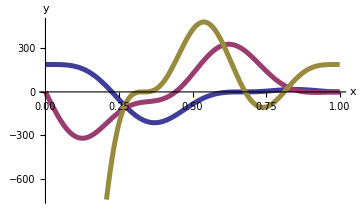
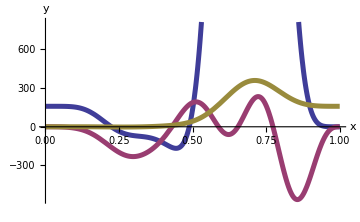

2

0.07

9.07683

3.90701

0.515965

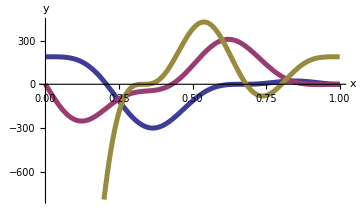
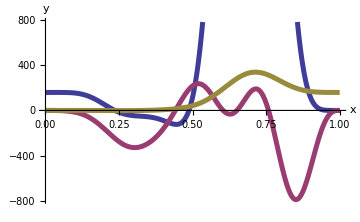

3

-0.07

0.0687303

11.6325

0.119337

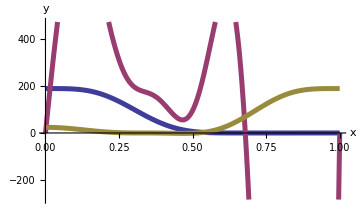
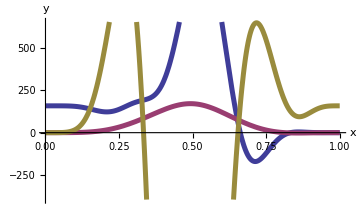

4

-0.07-5.82029×10^-14 ⅈ

0.0788166-0.005875 ⅈ

-0.245668-5.45293 ⅈ

0.0644584+0.00986061 ⅈ

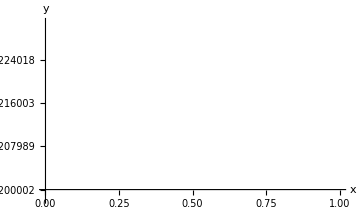
-Graphics--Graphics-

5

-0.07+5.82029×10^-14 ⅈ

0.0788166+0.005875 ⅈ

-0.245668+5.45293 ⅈ

0.0644584-0.00986061 ⅈ

-Graphics--Graphics-

6

0.07

1.25458

4.21551

0.213954

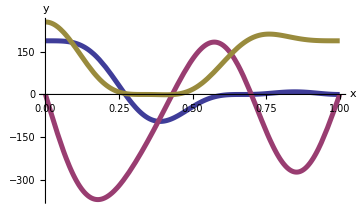
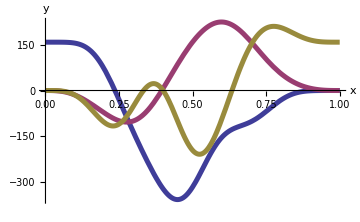

7

0.07-1.02431×10^-14 ⅈ

0.685413-0.135149 ⅈ

8.67578+10.3224 ⅈ

0.170606-0.00593296 ⅈ

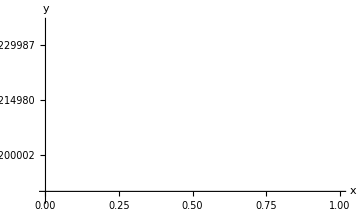
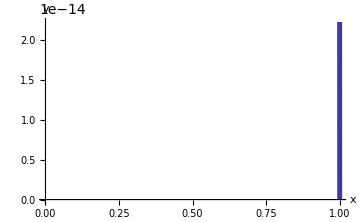

8

0.07+1.02431×10^-14 ⅈ

0.685413+0.135149 ⅈ

8.67578-10.3224 ⅈ

0.170606+0.00593296 ⅈ

-Graphics--Graphics-

9

-0.07

0.061965

1.91341

0.532592

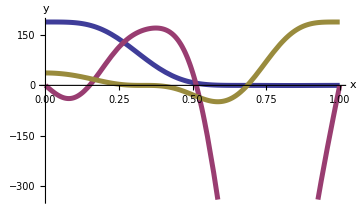
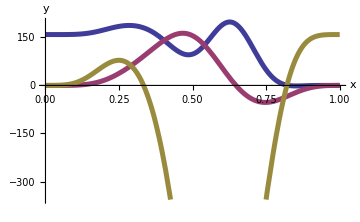

10

-0.07-1.0894×10^-12 ⅈ

-0.190102-0.124079 ⅈ

3.87225+2.39223 ⅈ

0.0620974-0.0125445 ⅈ

-Graphics--Graphics-

11

-0.07+1.0894×10^-12 ⅈ

-0.190102+0.124079 ⅈ

3.87225-2.39223 ⅈ

0.0620974+0.0125445 ⅈ

-Graphics--Graphics-

12

-0.07

0.105667

0.557847

0.34611

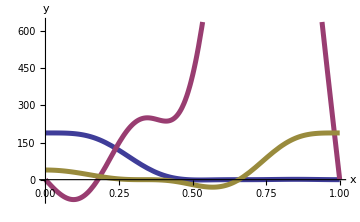
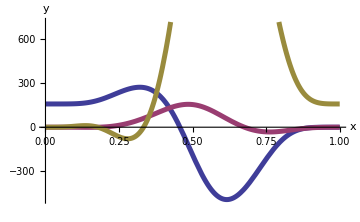

13

0.07-6.05765×10^-14 ⅈ

0.0613942+0.00148622 ⅈ

-0.115317+2.18647 ⅈ

0.56732-1.15086 ⅈ

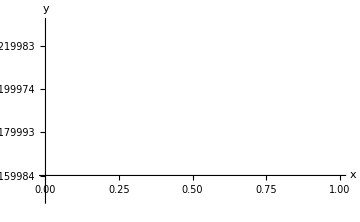
-Graphics--Graphics-

14

0.07+6.05765×10^-14 ⅈ

0.0613942-0.00148622 ⅈ

-0.115317-2.18647 ⅈ

0.56732+1.15086 ⅈ

-Graphics--Graphics-

15

-0.07

3.78527

15.3381

0.139878

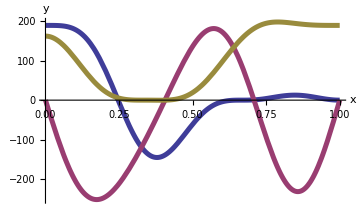
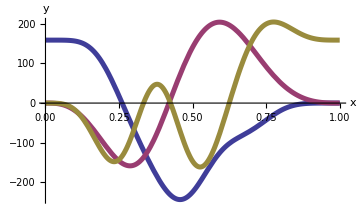

16

-0.07

1.91585

25.6461

0.108865

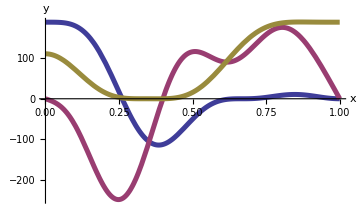
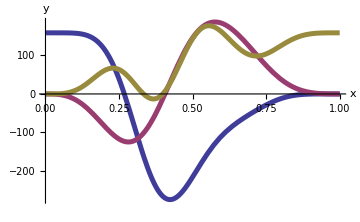

17

-0.07

2.20507

48.1282

0.112399

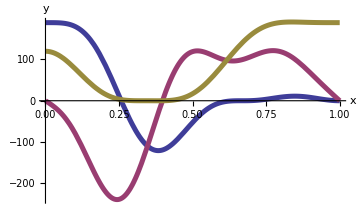
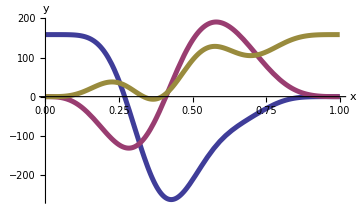

18

0.07

0.0451775

0.217341

0.0475755

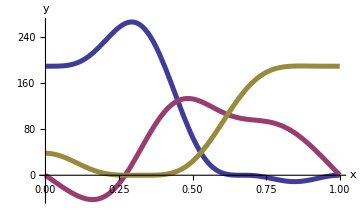
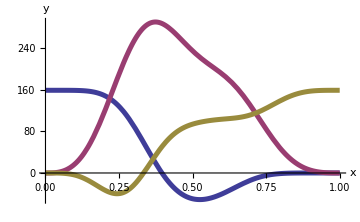

19

-0.07

0.059386

5.10306

15.8234

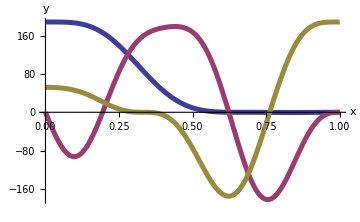
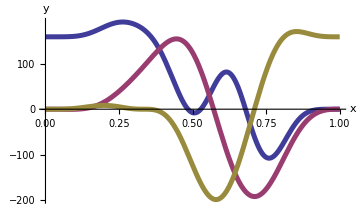

20

-0.07-8.39393×10^-13 ⅈ

-0.0256529-0.563979 ⅈ

-2.29479+1.84237 ⅈ

0.0921963+0.0113623 ⅈ

-Graphics--Graphics-

21

-0.07+8.39393×10^-13 ⅈ

-0.0256529+0.563979 ⅈ

-2.29479-1.84237 ⅈ

0.0921963-0.0113623 ⅈ

-Graphics--Graphics-

22

0.07+1.48014×10^-12 ⅈ

-0.150537-0.0944375 ⅈ

-0.405118+0.758541 ⅈ

0.069843+0.0403826 ⅈ

-Graphics--Graphics-

23

0.07-1.48014×10^-12 ⅈ

-0.150537+0.0944375 ⅈ

-0.405118-0.758541 ⅈ

0.069843-0.0403826 ⅈ

-Graphics--Graphics-

24

0.07

0.0312047

0.603888

0.0460531

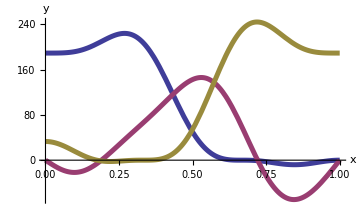
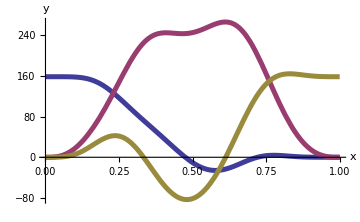

25

-0.07-1.81911×10^-11 ⅈ

-0.129118-0.705141 ⅈ

5.87198+3.33206 ⅈ

0.0530779-0.00416414 ⅈ

-Graphics--Graphics-

26

-0.07+1.81911×10^-11 ⅈ

-0.129118+0.705141 ⅈ

5.87198-3.33206 ⅈ

0.0530779+0.00416414 ⅈ

-Graphics--Graphics-

27

0.07-2.26662×10^-13 ⅈ

0.0222128+0.0000108068 ⅈ

0.163343-0.130832 ⅈ

0.0249919-0.00729187 ⅈ

-Graphics--Graphics-

28

0.07+2.26662×10^-13 ⅈ

0.0222128-0.0000108068 ⅈ

0.163343+0.130832 ⅈ

0.0249919+0.00729187 ⅈ

-Graphics--Graphics-

29

0.07+4.42293×10^-13 ⅈ

0.0694416-0.0160248 ⅈ

-0.0717171-0.65881 ⅈ

0.102915+0.0467197 ⅈ

-Graphics--Graphics-

30

0.07-4.42293×10^-13 ⅈ

0.0694416+0.0160248 ⅈ

-0.0717171+0.65881 ⅈ

0.102915-0.0467197 ⅈ

-Graphics--Graphics-

31

0.07+8.25845×10^-13 ⅈ

0.0526158-0.0599561 ⅈ

-0.442385-0.0923564 ⅈ

0.110892+0.0743243 ⅈ

-Graphics--Graphics-

32

0.07-8.25845×10^-13 ⅈ

0.0526158+0.0599561 ⅈ

-0.442385+0.0923564 ⅈ

0.110892-0.0743243 ⅈ

-Graphics--Graphics-

33

0.07-1.58931×10^-12 ⅈ

0.0482089-0.0168068 ⅈ

-1.46514-0.384491 ⅈ

-0.0430713+0.647121 ⅈ

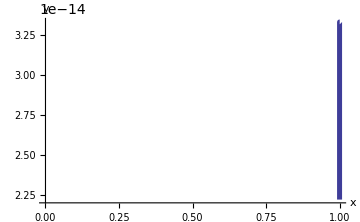
-Graphics--Graphics-

34

0.07+1.58931×10^-12 ⅈ

0.0482089+0.0168068 ⅈ

-1.46514+0.384491 ⅈ

-0.0430713-0.647121 ⅈ

-Graphics--Graphics-

35

-0.07-2.4506×10^-12 ⅈ

0.0358928-0.00853491 ⅈ

-0.613509+0.0535121 ⅈ

-0.0525564+0.25586 ⅈ

-Graphics--Graphics-

36

-0.07+2.4506×10^-12 ⅈ

0.0358928+0.00853491 ⅈ

-0.613509-0.0535121 ⅈ

-0.0525564-0.25586 ⅈ

-Graphics--Graphics-

37

-0.07

0.0260546

0.350392

0.019444

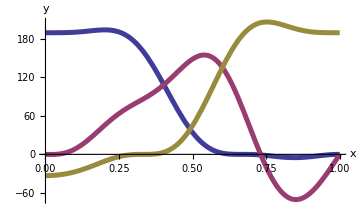
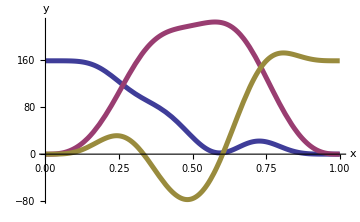

38

-0.07-3.08071×10^-13 ⅈ

0.0310963-0.00467296 ⅈ

-0.0846199-0.022407 ⅈ

0.0248855+0.0519925 ⅈ

-Graphics--Graphics-

39

-0.07+3.08071×10^-13 ⅈ

0.0310963+0.00467296 ⅈ

-0.0846199+0.022407 ⅈ

0.0248855-0.0519925 ⅈ

-Graphics--Graphics-

40

-0.07

0.0320075

0.0280597

0.0213629

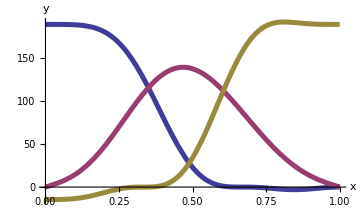
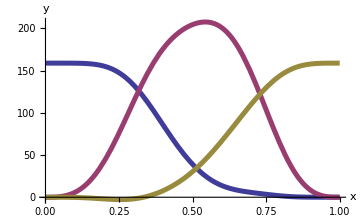

41

0.07

0.0626492

5.0914

1.02853

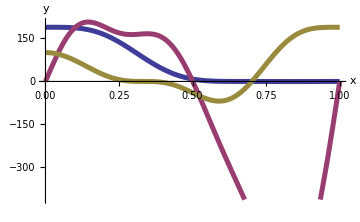
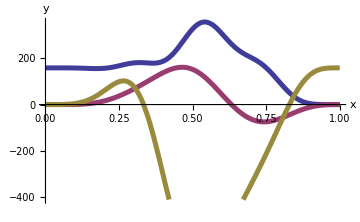

42

0.07

0.139638

0.0965359

0.372667

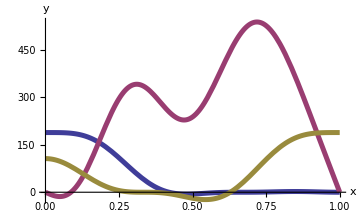
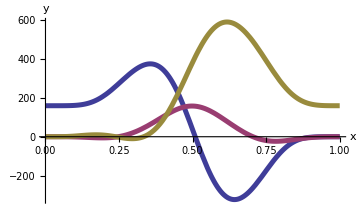

43

-0.07+5.51473×10^-13 ⅈ

0.0474181-0.0610085 ⅈ

-1.0131-5.79127 ⅈ

0.083242+0.0171824 ⅈ

-Graphics--Graphics-

44

-0.07-5.51473×10^-13 ⅈ

0.0474181+0.0610085 ⅈ

-1.0131+5.79127 ⅈ

0.083242-0.0171824 ⅈ

-Graphics--Graphics-

```mathematica
ph=100*(h[0]+2*Sum[h[i]*Cos[Pi*i*x],{i,1,K}]);
pb=100*2*Sum[b[i]*Sin[Pi*i*x],{i,1,L}];
pg=100*(g[0]+2*Sum[g[i]*Cos[Pi*i*x],{i,1,M}]);
pkh=100*(kh[0]+2*Sum[kh[i]*Cos[Pi*i*x],{i,1,K1}]);
pkb=100*2*Sum[kb[i]*Sin[Pi*i*x],{i,1,L1}];
pkg=100*(kg[0]+2*Sum[kg[i]*Cos[Pi*i*x],{i,1,M1}]);
pkhh=ph*pkh/300;
pkbb=pb*pkb/300;
pkgg=pg*pkg/300;

Do[Print[kk];
ssh=Sqrt[Sum[(h[Abs[i]]/.NSLv[[kk]])^2,{i,-K,K}]];
ssb=Sqrt[Sum[(b[Abs[i]]/.NSLv[[kk]])^2,{i,-L,L}]];
ssg=Sqrt[Sum[(g[Abs[i]]/.NSLv[[kk]])^2,{i,-M,M}]];
Print[((h[0]/.NSLv[[kk]])*(g[0]/.NSLv[[kk]])+2*(h[1]/.NSLv[[kk]])*(g[1]/.NSLv[[kk]]))/(ssh*ssg)];
Print[Sum[(h[i]/.NSLv[[kk]])^2,{i,2,K}]/((h[0]/.NSLv[[kk]])^2+2*(h[1]/.NSLv[[kk]])^2)];
Print[Sum[(b[i]/.NSLv[[kk]])^2,{i,2,L}]/((b[0]/.NSLv[[kk]])^2+2*(b[1]/.NSLv[[kk]])^2)];
Print[Sum[(g[i]/.NSLv[[kk]])^2,{i,2,M}]/((g[0]/.NSLv[[kk]])^2+2*(g[1]/.NSLv[[kk]])^2)];
Print[Plot[{ph/.NSLv[[kk]],pb/.NSLv[[kk]],pg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium],Plot[{pkh/.NSLv[[kk]],pkb/.NSLv[[kk]],pkg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]},ImageSize->Medium]],{kk,Length[NSLv]}]
(*kk=14;
Plot[{ph/.NSLv[[kk]],pb/.NSLv[[kk]],pg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkh/.NSLv[[kk]],pkb/.NSLv[[kk]],pkg/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
Plot[{pkhh/.NSLv[[kk]],pkbb/.NSLv[[kk]],pkgg/.NSLv[[kk]],(pkhh+pkbb+pkgg)/.NSLv[[kk]]},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]*)
```

11

0.	0.0000812236	0.	0.0000540336	0.	-0.0000470757

0.	-0.000411828	0.	-0.000273966	0.	0.000238688

0.	0.000107057	0.	0.0000712195	0.	-0.0000620485

0.	0.00091449	0.	-0.000815896	0.	-0.000671062

0.	0.0016123	0.	0.00829397	0.	-0.000219346

0.0123629	0.00762182	-0.00151849	0.00319313	0.0195878	-0.00460337

-0.00810589	-0.00257065	0.00475089	-0.0337432	-0.00853267	0.00924183

-0.0573942	-0.0434293	0.0260899	0.0239495	-0.069081	-0.0249847

-0.0494516	-0.0572617	0.153701	-0.192827	0.0783513	0.0322635

0.155318	0.100785	-0.0473184	-0.052845	0.0954987	0.146139

0.499683	0.482119	-0.688063	0.687905	-0.509985	-0.499947

0.663679	0.717215	0.	0.	0.662462	0.685303

0.499683	0.482119	0.688063	-0.687905	-0.509985	-0.499947

0.155318	0.100785	0.0473184	0.052845	0.0954987	0.146139

-0.0494516	-0.0572617	-0.153701	0.192827	0.0783513	0.0322635

-0.0573942	-0.0434293	-0.0260899	-0.0239495	-0.069081	-0.0249847

-0.00810589	-0.00257065	-0.00475089	0.0337432	-0.00853267	0.00924183

0.0123629	0.00762182	0.00151849	-0.00319313	0.0195878	-0.00460337

0.	0.0016123	0.	-0.00829397	0.	-0.000219346

0.	0.00091449	0.	0.000815896	0.	-0.000671062

0.	0.000107057	0.	-0.0000712195	0.	-0.0000620485

0.	-0.000411828	0.	0.000273966	0.	0.000238688

0.	0.0000812236	0.	-0.0000540336	0.	-0.0000470757

-0.07

0.0094415

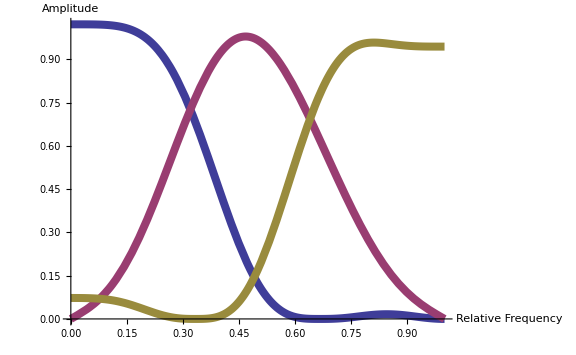

d:\plot2.eps

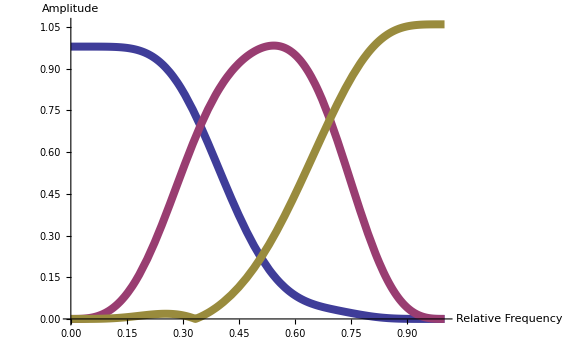

d:\plot1.eps

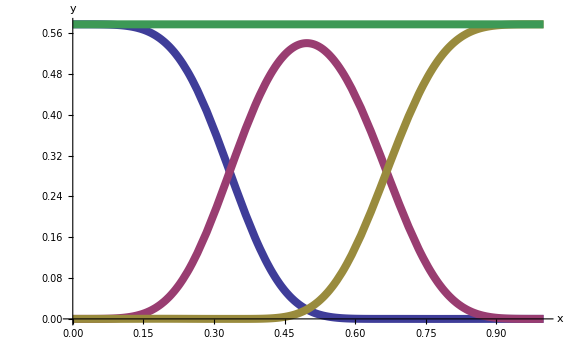

```mathematica
kk=40;(* 0.05 - 20 28 33 *) (* 0.01 - 25 *) (* 0 - 12 13 *) (* 0.03 - 24 27 28 *) (* 0.07 - 20 26 27 *) (* 0.1 - 20 29 30 31 34 *)
(*fs=OpenWrite["D:\Documents\Wavelets\W3 777 s014.txt",PageWidth->200]
SetOptions[fs, FormatType->StandardForm,CharacterEncoding-> "ASCII"]*)
KLM2=Max[K,K1,L,L1,M,M1]
min=10^-12;

Array[h2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,h2[i]=0.0];
For[i=-K,i≤K,i++,h2[i]=h[Abs[i]]/.NSLv[[kk]]];
Array[kh2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kh2[i]=0.0];
For[i=-K1,i≤K1,i++,kh2[i]=kh[Abs[i]]/.NSLv[[kk]]];
shh=Sqrt[Sum[h2[i]^2,{i,-K,K}]];
skh=Sqrt[Sum[kh2[i]^2,{i,-K1,K1}]];

Array[g2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,g2[i]=0.0];
For[i=-M,i≤M,i++,g2[i]=g[Abs[i]]/.NSLv[[kk]]];
Array[kg2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kg2[i]=0.0];
For[i=-M1,i≤M1,i++,kg2[i]=kg[Abs[i]]/.NSLv[[kk]]];
shg=Sqrt[Sum[g2[i]^2,{i,-M,M}]];
skg=Sqrt[Sum[kg2[i]^2,{i,-M1,M1}]];

Array[b2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,b2[i]=0.0];
For[i=-L,i≤L,i++,b2[i]=Sign[i]* b[Abs[i]]/.NSLv[[kk]]];
Array[kb2,2*KLM2+1,-KLM2];
For[i=-KLM2,i≤KLM2,i++,kb2[i]=0.0];
For[i=-L1,i≤L1,i++,kb2[i]=-Sign[i]*kb[Abs[i]]/.NSLv[[kk]]];
shb=Sqrt[Sum[b2[i]^2,{i,-L,L}]];
skb=Sqrt[Sum[kb2[i]^2,{i,-L1,L1}]];

(* нормировка по обратным функциям *)
(*For[i=-K,i≤K,i++,ss=h2[i]*skh;h2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-K1,i≤K1,i++,ss=kh2[i]/skh;kh2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M,i≤M,i++,ss=g2[i]*skg;g2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M1,i≤M1,i++,ss=kg2[i]/skg;kg2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L,i≤L,i++,ss= b2[i]*skb;b2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L1,i≤L1,i++,ss=kb2[i]/skb;kb2[i]=If[Abs[ss]<min,0.0,ss]];*)

(* нормировка по прямым функциям *)
For[i=-K,i≤K,i++,ss=h2[i]/shh;h2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-K1,i≤K1,i++,ss=kh2[i]*shh;kh2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M,i≤M,i++,ss=g2[i]/shg;g2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-M1,i≤M1,i++,ss=kg2[i]*shg;kg2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L,i≤L,i++,ss= b2[i]/shb;b2[i]=If[Abs[ss]<min,0.0,ss]];
For[i=-L1,i≤L1,i++,ss=kb2[i]*shb;kb2[i]=If[Abs[ss]<min,0.0,ss]];

(*For[i=-KLM2,i≤KLM2,i++,Print[kh2[i]]];*)
sep="\t";
(*For[i=-KLM2,i≤KLM2,i++,WriteString[fs,h2[i],sep,kh2[i],sep,b2[i],sep,kb2[i],sep,g2[i],sep,kg2[i],"\n"]];
Close[fs];*)
For[i=-KLM2,i≤KLM2,i++,Print[h2[i],sep,kh2[i],sep,b2[i],sep,kb2[i],sep,g2[i],sep,kg2[i]]];


ampl=1.0/Sqrt[3];
ph2=ampl*(h2[0]+2*Sum[h2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pb2=ampl*2*Sum[b2[i]*Sin[Pi*i*x],{i,1,KLM2}];
pg2=ampl*(g2[0]+2*Sum[g2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkh2=ampl*(kh2[0]+2*Sum[kh2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkb2=-ampl*2*Sum[kb2[i]*Sin[Pi*i*x],{i,1,KLM2}];
pkg2=ampl*(kg2[0]+2*Sum[kg2[i]*Cos[Pi*i*x],{i,1,KLM2}]);
pkhh2=ph2*pkh2/(ampl*3);
pkbb2=pb2*pkb2/(ampl*3);
pkgg2=pg2*pkg2/(ampl*3);

Needs["PlotLegends`"];

Print[h2[0]*g2[0]+2*h2[1]*g2[1]];
Print[kh2[0]*kg2[0]+2*kh2[1]*kg2[1]];
plot2=Plot[{Abs[ph2],Abs[pb2],Abs[pg2]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MF","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.4,-0.3},LegendSize->0.5,LegendShadow->None]
Export["d:\plot2.eps",plot2]
plot1=Plot[{Abs[pkh2],Abs[pkb2],Abs[pkg2]},{x,0,1},AxesLabel->{"Relative Frequency","Amplitude"},PlotLegend->{"LF","MF","HF"},
LabelStyle->Directive[FontFamily->"Times",FontSize->14],PlotStyle->{Thickness[0.01]},AxesStyle->Thick,ImageSize->Large,LegendPosition->{0.4,-0.3},LegendSize->0.5,LegendShadow->None]
Export["d:\plot1.eps",plot1]
Plot[{pkhh2,pkbb2,pkgg2,(pkhh2+pkbb2+pkgg2)},{x,0,1},AxesLabel->{"x","y"},
LabelStyle->Directive[FontFamily->"Times",FontSize->12],PlotStyle->{Thickness[0.01]}]
```